```mathematica
(* By István Zachar *)
(* istvan.zachar80@gmail.com *)
(* 2016 *)
(* Mathematica 11.0.0.0 *)
```

## Functions

```mathematica
SortNatural[list_List]:=Module[{tmp},
tmp=StringSplit[ToString/@list,x:NumberString:>ToExpression@x];
list[[Ordering@PadRight@tmp]]
];
```

## Code

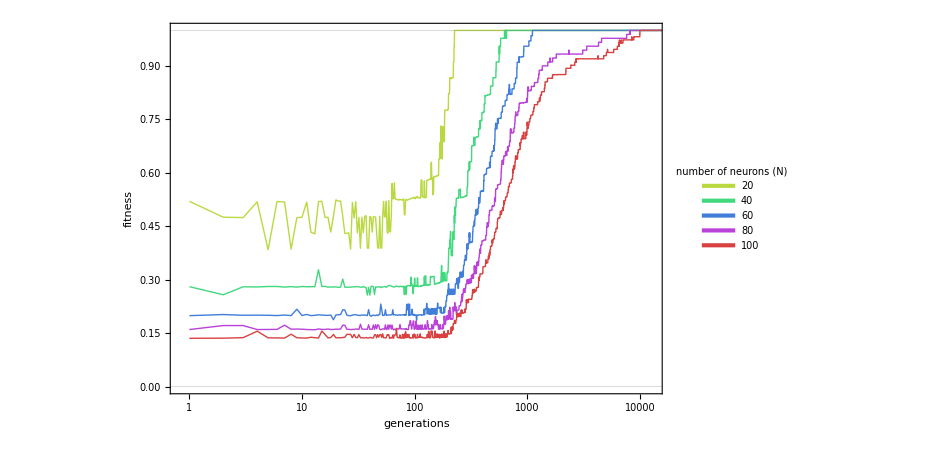

Save figure

```mathematica
dir=NotebookDirectory[]; (* Directory to red files from and save image to *)
name="combined"; (* file name to save image to *)

mask="("~~NumberString~~")"~~EndOfString;
time=1;(* column index of time variable *)
column=2; (* index of column to take; uses Part. *)
rows=All(*501;;-1;;1000*);(* index of rows to take: All; 501;;-1;;1000: takes every 500th row, starting from 501. Uses Take. *)
combine=Mean; (* False|None or Mean; only, if each series in a group is extended to the same length *) 
extend=All;(* False|None, Automatic = extending to maximum of each group, All = extending to maximum of all groups *)


columns=DeleteDuplicates@Join[{time},{column}];
files=SortNatural@FileNames["*.dat",{dir}];
ts=FileBaseName@#->TimeSeries@(Take[Part[#,columns]&/@Import[#,"Table"],rows])&/@files; (* uncollapsed data *)
Length@ts;

groups=If[MatchQ[combine,False|None],List/@Association@@ts,Values/@GroupBy[ts,StringReplace[First@#,mask->""]&]];
groups=If[MatchQ[extend,False|None],groups,
max=Map[#["LastTime"]&,groups,{2}];
max=Switch[extend,False|None,max,True|Automatic,(#/.(_Integer->Max@#))&/@max,All,(#/.(_Integer->Max@#))&@max];
MapThread[TimeSeriesInsert[#1,{#2,#1@"LastValue"}]&,{groups,max},2]];
data=If[MatchQ[combine,False|None],First/@groups,combine/@groups];(* collapsed data *)



opts={PlotTheme->"Scientific",PlotStyle->Thick, PlotRange->{{0,All},{0,1}},PlotRangePadding->{Scaled@.02,Scaled@.03},ImageSize->700,
Joined->True,PlotStyle->Thick,LabelStyle->Directive[Black,18,FontFamily->"Helvetica"],Background->White,GridLines->{None,{0,1}},FrameStyle->Black,ImagePadding->{{30,1},{30,1}}};

(* Subimage *)
data2=Values[#@"Path"&/@data];
last=data2[[All,-1,1]];
data2=MapThread[Join,{data2,Table[{{last[[i]],1.},{last[[i]]+10000,1.}},{i,Length@data2}]}];

pos={.88,.3};
n=Length@data2;
{sx,sy}={700,400};
inset=Rasterize[Block[{d=Import["C:\\Zac\\Science\\NRH\\Storkey\\meta\\TYPE4_NN10_Nchg_P10_andras\\dat80_0.dat","Table"]},
ListLogLinearPlot[Prepend[d,{1,.162851}],PlotTheme->"Scientific",PlotStyle->AbsoluteThickness@4,Background->White,Joined->True,PlotRange->{{1,All},{0,1}},FrameStyle->Directive[Black,AbsoluteThickness@2],LabelStyle->Directive[24,Black],ImagePadding->All,opts]],RasterSize->500];
plot=ListLogLinearPlot[data2,
PlotStyle->Table[Directive[Thick,Hue[i/N@n,.7,.85]],{i,n}],
FrameLabel->{"generations","fitness"},
PlotRange->{{1,13000},{.0000001,1}},ImagePadding->All,
PlotLegends->Placed[LineLegend[Table[Directive[AbsoluteThickness@3,Hue[i/N@n,.7,.85]],{i,n}],{20,40,60,80,100},LegendLabel->"number of\nneurons (N)"],pos],
Epilog->{Inset[inset,{0,.57},Scaled@{0,0},4.1]},ImageSize->700,AspectRatio->1/1.5,FrameStyle->Black,
opts];

plot
Column@{
InputField[Dynamic@name,String,BaseStyle->Black],
Button[Style["Save figure",Black],Export[FileNameJoin@{dir,name<>".tiff"},plot,"TIFF",ImageResolution->600,"ImageEncoding"->"LZW","CompressionLevel"->1]]
}
```